Sonido

En Wolfram Language, al sonido se le da un tratamiento muy parecido al de las gráficas, salvo que, en vez de manejar cosas tales como círculos, se manejan
notas musicales. Se pulsa el botón de reproducción  para, en efecto, reproducir sonidos. A menos que se especifique otra cosa, Wolfram Language hace que las notas suenen como si estuvieran tocadas en un piano.

Genere una nota do central (C central):

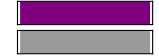

```mathematica
Sound[SoundNote["C"]]
```

Puede especificarse una secuencia de notas escribiéndolas en una lista.

Toque tres notas consecutivas:

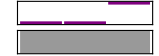

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["G"]}]
```

En vez de dar los nombres de las notas puede darse un número para especificar su tono. Do central corresponde al 0. Por cada semitono por encima del do central, el número aumenta en 1. El sol central se encuentra a 7 semitonos arriba del do central, así que está especificado por el número 7. (Una octava consta de 12 semitonos.)

Especifique las notas con números:

```mathematica
Sound[{SoundNote[0],SoundNote[0],SoundNote[7]}]
```

-Graphics-

Use Table para generar una secuencia de 5 notas:

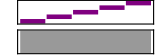

```mathematica
Sound[Table[SoundNote[n],{n,5}]]
```

Si no se dice otra cosa, cada nota dura 1 segundo. Use SoundNote[tono,duración] para obtener una duración diferente.

Reproduzca cada nota por 0.1 segundos:

```mathematica
Sound[Table[SoundNote[n,0.1],{n,5}]]
```

-Graphics-

Además del piano, SoundNote puede producir el sonido en una amplia gama de instrumentos. El nombre de cada instrumento es una cadena de caracteres.

Reproduzca notas de un violín simulado:

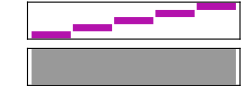

```mathematica
Sound[Table[SoundNote[n,0.1,"Violin"],{n,5}]]
```

Es muy sencillo tocar “música aleatoria”, es decir, que sea diferente cada vez que se genera.

Toque una secuencia de 20 notas con tonos aleatorios:

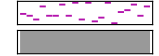

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1,"Violin"],20]]
```

Vocabulario

Sound[{...}] |   | crea un sonido a base de notas 
SoundNote["C"] |   | una nota por su nombre en inglés 
SoundNote[5] |   | una nota con tono numerado 
SoundNote[5,0.1] |   | una nota de duración especificada 
SoundNote[5,0.1,"Guitar"] |   | un nota tocada en un instrumento dado

"10 Exercises Available"
"with 4 extras" | "Get Started »"

Genere la sucesión de las notas con tonos 0, 4 y 7. »

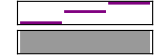
| Expected output: |  
  | -Graphics- |

Reproduzca durante 2 segundos el sonido de la en un violonchelo. »

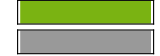
| Expected output: |  
  | -Graphics- |

Genere un “riff” de notas de tonos entre el 0 y el 48, en incrementos de 1, cada una con duración de 0.05 segundos. »

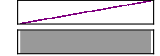
| Expected output: |  
  | -Graphics- |

Genere una secuencia de notas bajando desde el tono 12 hasta el 0 en incrementos de 1. »

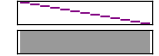
| Expected output: |  
  | -Graphics- |

Genere una secuencia de notas a partir del do central, subiendo sucesivamente de octava en octava. »

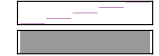
| Expected output: |  
  | -Graphics- |

Genere una secuencia de 10 notas en una trompeta con tonos aleatorios del 0 al 12, cada uno de duración 0.2 segundos. »

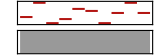
| Sample expected output: |  
  | -Graphics- |

Genere una secuencia de 10 notas con tonos aleatorios hasta el 12 y duraciones aleatorias hasta de 10 décimas de segundo. »

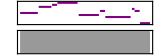
| Sample expected output: |  
  | -Graphics- |

Genere notas de 0.1 segundo de duración y de tonos dados por los dígitos de 2^31. »

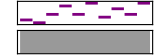
| Expected output: |  
  | -Graphics- |

Cree un sonido con las letras de CABBAGE, cada una con duración de 0.3 segundos y con el sonido de una guitarra. »

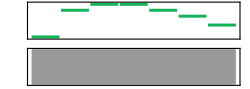
| Expected output: |  
  | -Graphics- |

Genere notas con duración de 0.1 segundos con tonos dados por los números de letra de los caracteres en “wolfram”. »

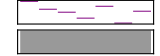
| Expected output: |  
  | -Graphics- |

Reproduzca la secuencia de tres notas Re central tocadas en violonchelo, piano y guitarra, con una duración de 1 segundo.  »

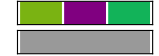
| Expected output: |  
  | -Graphics- |

Genere una secuencia de notas desde el tono 0 hasta el tono 12, subiendo en incrementos de 3.  »

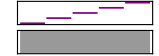
| Expected output: |  
  | -Graphics- |

Genere una secuencia de notas a partir del do central, subiendo sucesivamente en una quinta justa (7 semitonos) cada vez.  »

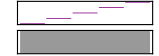
| Expected output: |  
  | -Graphics- |

Genere notas de 0.02 segundos cuyos tonos sean las longitudes de los nombres de los enteros del 1 al 200. »

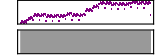
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Cómo saber qué instrumentos musicales están disponibles?

Vea la lista que aparece en “Detalles y opciones”, en la página de referencia de SoundNote, o simplemente comience a escribir para ver las opciones de autocompletado que se ofrecen. Puede usarse también la numeración de los instrumentos, del 1 al 128. Ahí se encuentran todos los instrumentos MIDI estándar, incluyendo las percusiones.

¿Cómo se tocan las notas por debajo del do central?

Simplemente se usan números negativos, como en SoundNote[-10].

¿Cómo se les llama a las notas sostenidas y bemoles?

Mi# (mi sostenido), lab (la bemol), etc. También están numeradas (e.g. Mi# es 5). El # y el b pueden escribirse como caracteres ordinarios de teclado (aunque también están disponibles los caracteres especiales ♯ y ♭ ).

¿Cómo se construye un acorde?

Se ponen los nombres de las notas en una lista, como en SoundNote[{"C","G"}].

¿Cómo se introduce un silencio?

Para un silencio de 0.2 segundos, se usa SoundNote[None,0.2].

¿Cómo hacer para que se emita un sonido inmediatamente, sin tener que oprimir el botón de reproducción?

Use EmitSound, como en EmitSound[Sound[SoundNote["C"]]], etc.

¿Por qué se requieren las comillas al nombrar una nota como “C”?

Porque el nombre de la nota es una cadena en Wolfram Language. Si se escribiera solamente C, se inter.08pretaría como una función llamada C, que no es lo que se desea.

¿Puede grabarse audio y manipularlo?

Sí. Use AudioCapture y, luego, funciones como AudioPlot, Spectrogram, AudioPitchShift, etc.

Notas técnicas

SoundNote corresponde a sonido MIDI. Wolfram Language también soporta el “sonido muestreado”, usando, por ejemplo, funciones como ListPlay, así como una construcción de Audio que representa todos los aspectos de una señal de audio.

Para obtener salida hablada, use Speak. Para hacer un beep, use Beep.

Para explorar más

Guía para generación de sonido en Wolfram Language »